```mathematica
SetDirectory[NotebookDirectory[]];<<Developer`;$HistoryLength=0;
```

### Misc

```mathematica
Transpose@Table[Flatten@Table["0x"<>IntegerString[2^Range[0,63].#,16,16]<>"u"&@Flatten@Table[If[i==i0&&j==j0,0,If[Normalize@{i-i0,j-j0}==Normalize@dir,1,0]],{i,1,8},{j,1,8}],{i0,8},{j0,8}],{dir,{{1,1},{1,0},{1,-1},{0,1},{0,-1},{-1,1},{-1,0},{-1,-1}}}]
```

```mathematica
Table[RepeatedTiming[Dimensions[c.(b1.(b2.(b3.(b4.(a.x[[;;,;;i]])))))]][[1]]/i*10^6,{i,{1,2,4,8,16,32,64,128,256}}]
```

{38.,43.,24.,16.,12.,8.07,7.,6.13,5.88}

### Net

```mathematica
net=NetInitialize@NetGraph[{NetChain[{256,Ramp,256,Ramp,256,Ramp,256,Ramp}],NetChain[{256,Ramp,64}],NetGraph[{ThreadingLayer[Plus],SoftmaxLayer[]},{{NetPort["x"],NetPort["y"]}->1->2}],NetChain[{64,Ramp,1,Tanh}]},{NetPort["Board"]->1,1->2->NetPort[3,"x"],NetPort["Mask"]->NetPort[3,"y"],3->NetPort["Policy"],1->4->NetPort["Value"]},"Board"->64,"Mask"->64];
```

```mathematica
ClearAll[savenet]
```

```mathematica
apply[weights_,biases_,input_,f_:Identity]:=f[weights.input+biases];
```

```mathematica
input=Normal@SparseArray[{28->-1.,29->1.,36->1.,37->-1.},64,0.];
mask=Normal@SparseArray[{20->0.,27->0.,38->0.,45->0.},64,-999.];
```

```mathematica
net[<|"Board"->input,"Mask"->mask|>]
```

<|Policy→{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.277047,0.,0.,0.,0.,0.,0.,0.289999,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.191759,0.,0.,0.,0.,0.,0.,0.241196,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},Value→{0.197344}|>

### Import games

```mathematica
getgame[str_,length_]:=NumericArray[#,"Real32"]&/@Transpose@
Table[{selfmask,oppomask,movemask}=BinaryReadList[str,"UnsignedInteger64",3];policies=BinaryReadList[str,"UnsignedInteger8",31];result=N@BinaryReadList[str,"Integer8",1];board=N[IntegerDigits[selfmask,2,64]-IntegerDigits[oppomask,2,64]];
policies=Normal@SparseArray[Thread[#->(#/Clip[Total@#,{1.,∞}]&@Reverse[policies[[;;Length@#]]+0.5])]&@SparseArray[IntegerDigits[movemask,2,64]]["NonzeroPositions"],64,0.0];If[i≠1&&movemask≠0,{board,policies,result},Nothing],{i,length}];
```

```mathematica
getfile[file_]:=Block[{str=OpenRead[file,BinaryFormat->True],games},games=Join[Sequence@@Reap[While[TrueQ[0<(length=BinaryRead[str,"UnsignedInteger64"])<120],Sow[getgame[str,length]]]][[2,1]],2];Close[file];games];
getfiles[files_]:=Join[Sequence@@(getfile/@files),2];
```

```mathematica
plotpos[board_,policy_,value_]:=Column[{"value = "<>ToString@Normal@value,Grid[Partition[MapThread[
If[#1>0,Style["●",45],If[#1<0,Style["○",45],If[#2>0,Style[ToString[#],Hue[0,1,#/50],15]&@Clip[Round[#2*100],{0,99}],""]]]&,{Normal@board,Normal@policy}],8],Frame->All,FrameStyle->Gray,Alignment->{Center,Center},ItemSize->{2,2.5}]}];
```

```mathematica
Manipulate[Grid[Partition[MapThread[
If[#1>0,Style["●",45],If[#1<0,Style["○",45],If[#2>0,Style[ToString[#],Hue[0,1,#/50],15]&@Clip[Round[#2*100],{0,99}],""]]]&,Normal/@games[[;;2,i]]],8],Frame->All,FrameStyle->Gray,Alignment->{Center,Center},ItemSize->{2,2.5}],{i,1,Length@games[[-1]],1}]
```

### Training

```mathematica
net=Import["nets/net-0.wlnet"];
games=Block[{perm=ToPackedArray[Join@@RandomSample[Partition[Range[Length@#[[1]]],UpTo[79]]]]},#[[perm]]&/@#]&@Uncompress@Import["games/games-0.txt"];
npositions=Length@games[[-1]]
```

109955

```mathematica
$orientations=ToPackedArray[Flatten/@{#,Reverse[#,{1}],Reverse[#,{2}],Reverse[#,{1,2}],Transpose@#,
Reverse[Transpose@#,{1}],Reverse[Transpose@#,{2}],Reverse[Transpose@#,{1,2}]}&@Partition[Range[64],8]];
SetAttributes[sampler,HoldFirst];
sampler[games_]:=Block[{pos=RandomInteger[{1,Length[games[[1]]]},#BatchSize/8]},<|
"Board"->Join@@Table[#[[;;,o]],{o,$orientations}]&@Normal@games[[1,pos]],
"Frequency"->Join@@Table[#[[;;,o]],{o,$orientations}]&@Normal@games[[2,pos]],
"Result"->Join@@ConstantArray[Normal@games[[3,pos]]/100.0,8]|>]&;
```

```mathematica
lossnet[net_]:=NetGraph[{net,MeanSquaredLossLayer[],CrossEntropyLossLayer["Probabilities"]},{NetPort["Board"]->NetPort[1,"Input"],
NetPort[1,"Value"]->2,NetPort["Result"]->NetPort[2,"Target"],NetPort[2,"Loss"]->NetPort["ValueLoss"],
NetPort[1,"Policy"]->3,NetPort["Frequency"]->NetPort[3,"Target"],NetPort[3,"Loss"]->NetPort["PolicyLoss"]
},"Board"->64,"Frequency"->64,"Result"->1,"ValueLoss"->"Real","PolicyLoss"->"Real"];
```

```mathematica
{trained,plots}=NetTrain[lossnet,sampler[1,0.9npositions],{"FinalNet","FinalPlots"},LossFunction->"Loss",ValidationSet->{validationset,"Interval"->200},BatchSize->4000,
Method->{"SGD","Momentum"->0.95,"LearningRate"->0.01,"L2Regularization"->0.0001,
"LearningRateSchedule"->(If[#<100,Clip[1.0-0.95^#,{0.0001,1.0}],1.0]&)},
MaxTrainingRounds->2000,TargetDevice->"GPU"];
newnet=NetExtract[trained,1];
```

```mathematica
newnetoutput[i_]:=newnet[<|"Board"->Normal@games[[1,i]],"Mask"->(If[#>0,0.0,-1000.0]&/@Normal@games[[2,i]])|>];
```

```mathematica
Manipulate[Row[{plotpos[Normal@games[[1,i]],Normal@games[[2,i]],Normal@games[[3,i]]]," ",plotpos[Normal@games[[1,i]],newnetoutput[i]["Policy"],newnetoutput[i]["Value"]]}],{i,1,npositions,1}]
```

```mathematica
policies=newnetoutput[#]["Policy"]&/@Range[100000,109000];
```

```mathematica
If[Length[#]==0,0.,Mean@#-1]&@Select[#,#>0&]&/@Transpose@(Total@UnitStep[#-0.000001]#&/@policies)
```

```mathematica
savenet["nets/net-1",newnet];
```

```mathematica
MatrixPlot[Partition[If[Length[#]==0,0.,Mean@#-1]&@Select[#,#>0&]&/@Transpose@(Total@UnitStep[#-0.000001]#&/@policies),8]]
```

### Runs

```mathematica
ClearAll[comparenets,savenet,getnet,getgames,deletetempgames,savegames,runselfplay,roundstr];
roundstr=IntegerString[#,10,4]&;
runselfplay[{run_,round_},ngames_,nthreads_,options_:{}]:=RunProcess[{"xargs","-n","1","-P",ToString[nthreads],"./othello","--mode","selfplay","--net-path",run<>"/nets/net-"<>roundstr[round],"--games",Round[ngames/nthreads],"--playouts",10000,"--temp-init",2.0,"--temp-slope",0.1,"--temp-final",0.0,"--policy-temp",1.2,"--kldgain-limit",0.0004,Sequence@@options,"--games-path"},All,StringRiffle[Table[run<>"/games/games-"<>roundstr[round]<>".bin."<>ToString[i],{i,1,nthreads}]," "]];
savegames[{run_,round_}]:=Export[run<>"/games/games-"<>roundstr[round]<>".txt",
Compress@getfiles[FileNames[run<>"/games/games-"<>roundstr[round]<>".bin.*"]]];
deletetempgames[{run_,round_}]:=If[FileSize[run<>"/games/games-"<>roundstr[round]<>".txt"]>Quantity[500,"Kilobytes"],
DeleteFile[FileNames[run<>"/games/games-"<>roundstr[round]<>".bin.*"]];];
getgames[run_,n_,m_:∞]:=Join[##,2]&@@@
Transpose[Block[{trainsize=Round[0.9Length[#[[1]]]]},{#[[;;,;;trainsize]],#[[;;,trainsize+1;;]]}]&@Uncompress@Import[#]&/@Echo@Take[Reverse@Take[FileNames[run<>"/games/games-*.txt"],UpTo[m]],UpTo[n]]];
getnet[{run_,round_}]:=Import[run<>"/nets/net-"<>roundstr[round]<>".wlnet"];
savenet[{run_,round_},net_]:=(CreateDirectory[run<>"/nets/net-"<>roundstr[round]];KeyValueMap[Export[run<>"/nets/net-"<>roundstr[round]<>"/"<>#1,Normal@#2,"Real32"]&,getnetparams[net]];
Export[run<>"/nets/net-"<>roundstr[round]<>".wlnet",net];);
comparenets[{oldrun_,oldround_},{newrun_,newround_},ngames_,nthreads_,print_:False,options_:{}]:=Table[StringCount[#,c],{c,{"w","d","l"}}]&@(If[TrueQ[print],Echo[#],#]&@RunProcess[{"xargs","-n","1","-P",ToString[nthreads],"./othello","--mode","compare","--net-path",newrun<>"/nets/net-"<>roundstr[newround],"--alt-net-path",oldrun<>"/nets/net-"<>roundstr[oldround],"--games",Round[ngames/nthreads],"--playouts",200,Sequence@@options},All,StringRiffle[ToString/@Range[nthreads]," "]])["StandardOutput"];
testnewnet[ngames_,nthreads_]:=Do[If[$round+1-diff≥$minround,
PutAppend[({$round+1,$round+1-diff}->comparenets[{$run,$round+1-diff},{$run,$round+1},ngames,nthreads]),$run<>"/testresults.txt"]],{diff,{1,3,10}}];
eloestimate[{win_,draw_,lose_}]:=Around[-400.Log10[#.{1,1,1}/#.{1.,0.5,0.}-1.]&/@Transpose[RandomVariate[PoissonDistribution[#],100]&/@{win,draw,lose}]]
$run="run5";
```

```mathematica
runselfplay[{$run,1},1,1,{"--playouts","10000","--kldgain-limit","0.0004"}]
```

<|ExitCode→0,StandardOutput→.time: 3369.582 ms
,StandardError→|>

```mathematica
Do[Echo@AbsoluteTiming[runselfplay[{$run,i},2500,5,{"--play-random","--playouts","4000"}];];savegames[{$run,i}];deletetempgames[{$run,i}];,{i,1,7}]
```

```mathematica
{games,validgames}=getgames["run5",1];
```

{run5/games/games-0213.txt}

```mathematica
StringRiffle[StringJoin[Alphabet[][[#2]],ToString@#1]&@@(QuotientRemainder[#-1,8]+1)&/@Flatten@BlockMap[Position[#[[2]]-#[[1]],1.0]&,Prepend[Abs@Normal@games[[1,53*4-52;;53*4]],Flatten@N@DiskMatrix[1,8]],2,1]," "]
```

f5 f6 e6 f4 g6 f7 g5 h6 e3 f2 h5 g4 h7 c5 c6 d3 c4 d6 e8 f8 e7 d8 h4 d7 c7 c3 c8 g7 e2 b3 b4 f3 h8 g8 c2 g3 d2 e1 h3 b1 c1 d1 a3 b2 a1 g2 h1 h2 g1 f1 a5 a4 a2

```mathematica
Manipulate[If[EvenQ@Round@Total[#1],plotpos[#1,#2,#3],plotpos[-#1,#2,-#3]]&@@games[[;;,i]],{i,1,Length[games[[1]]],1}]
```

```mathematica
Do[Echo[AbsoluteTiming[runselfplay[i,1000,5]]];
savegames[i];deletetempgames[i];,{i,1,9}]
```

```mathematica
Table[ArrayPlot[#/Clip[N@Total[#],{1.,∞}]&/@BinCounts[Transpose@{Flatten@validationset[[3]],Flatten@inet[validationset[[1]],TargetDevice->"GPU"]["Value"]},{Range[-1.025,1.025,0.05]},{Range[-1.025,1.025,0.05]}],ImageSize->300],{inet,{getnet[{$run,7}],getnet[{$run,70}],getnet[{$run,110}]}}]
```

```mathematica
$gamesperbatch=2500;
$symmetryfactor=8.0;
$netdependencylength=8;
$samplingratio=3.0;
$batchsize=4000;
$maxroundsfactor=$symmetryfactor/$batchsize/$netdependencylength*$samplingratio;
$minround=7;
validlistsdata={};
roundlistsdata={};
```

```mathematica
$round=7;
{games,validgames}=getgames[$run,8];$npositions=Length@games[[1]];
trainingsampler=sampler[games];validationset=sampler[validgames][<|"BatchSize"->80000|>];
```

{run3/games/games-0007.txt,run3/games/games-0006.txt,run3/games/games-0005.txt,run3/games/games-0004.txt,run3/games/games-0003.txt,run3/games/games-0002.txt,run3/games/games-0001.txt,run3/games/games-0000.txt}

```mathematica
(*DumpSave["dump/losshistory-run2.mx",{validlistsdata,roundlistsdata}];*)
```

```mathematica
(*Get["dump/losshistory.mx"];*)
```

```mathematica
{trained,validlists,roundlists}=NetTrain[lossnet[getnet[{$run,$round}]],trainingsampler,{"FinalNet","ValidationMeasurementsLists","RoundMeasurementsLists"},
LossFunction->{"ValueLoss"->Scaled[4.0],"PolicyLoss"},ValidationSet->{validationset,"Interval"->50},BatchSize->$batchsize,
Method->{"SGD","Momentum"->0.93,"LearningRate"->0.02,"L2Regularization"->0.0001,
"LearningRateSchedule"->(If[#<100,Clip[1.0-0.93^#,{0.00001,1.0}],1.0]&)},
MaxTrainingRounds->Round[$npositions*$maxroundsfactor],TargetDevice->"GPU"];
AppendTo[validlistsdata,validlists];AppendTo[roundlistsdata,ToPackedArray[Mean/@Partition[#,UpTo[50]]]&/@roundlists];
savenet[{$run,$round+1},NetExtract[trained,1]];
```

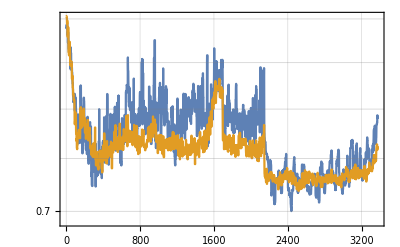
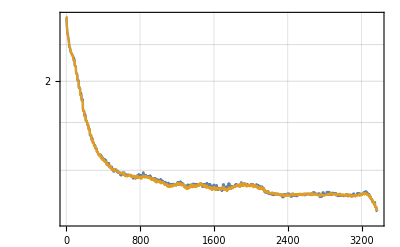

```mathematica
Row@Table[ListLinePlot[MedianFilter[#,3]&/@{Join@@(#[k[[1]]]&/@validlistsdata),Join@@(#[k[[1]]]&/@roundlistsdata)},PlotRange->k[[2]],ScalingFunctions->"Log",Frame->True,ImageSize->400,GridLines->Automatic],{k,{{"ValueLoss",{All,All}},{"PolicyLoss",{All,All}}}}]
```

```mathematica
Do[
$round=r;
Echo[Row[{"current round = ",$round}]];
Echo[AbsoluteTiming[StringCount[#,"."]&@runselfplay[{$run,$round},$gamesperbatch,5]["StandardOutput"]]];
savegames[{$run,$round}];deletetempgames[{$run,$round}];
{games,validgames}=getgames[$run,$netdependencylength];$npositions=Length@games[[1]];
trainingsampler=sampler[games];validationset=sampler[validgames][<|"BatchSize"->80000|>];
{trained,validlists,roundlists}=NetTrain[lossnet[getnet[{$run,$round}]],trainingsampler,{"FinalNet","ValidationMeasurementsLists","RoundMeasurementsLists"},
LossFunction->{"ValueLoss"->Scaled[4.0],"PolicyLoss"},ValidationSet->{validationset,"Interval"->50},BatchSize->$batchsize,
Method->{"SGD","Momentum"->0.96,"LearningRate"->0.002,"L2Regularization"->0.0001,
"LearningRateSchedule"->(If[#<100,Clip[1.0-0.96^#,{0.00001,1.0}],1.0]&)},
MaxTrainingRounds->Round[$npositions*$maxroundsfactor],TargetDevice->"GPU"];
AppendTo[validlistsdata,validlists];AppendTo[roundlistsdata,ToPackedArray[Mean/@Partition[#,UpTo[50]]]&/@roundlists];
savenet[{$run,$round+1},NetExtract[trained,1]];
testnewnet[400,5];
,{r,214,217}]
```

current round = 214

{1935.83,2505}

{run5/games/games-0214.txt,run5/games/games-0213.txt,run5/games/games-0212.txt,run5/games/games-0211.txt,run5/games/games-0210.txt,run5/games/games-0209.txt,run5/games/games-0208.txt,run5/games/games-0207.txt}

current round = 215

{1934.1,2505}

{run5/games/games-0215.txt,run5/games/games-0214.txt,run5/games/games-0213.txt,run5/games/games-0212.txt,run5/games/games-0211.txt,run5/games/games-0210.txt,run5/games/games-0209.txt,run5/games/games-0208.txt}

current round = 216

{1905.31,2505}

{run5/games/games-0216.txt,run5/games/games-0215.txt,run5/games/games-0214.txt,run5/games/games-0213.txt,run5/games/games-0212.txt,run5/games/games-0211.txt,run5/games/games-0210.txt,run5/games/games-0209.txt}

current round = 217

{1901.39,2505}

{run5/games/games-0217.txt,run5/games/games-0216.txt,run5/games/games-0215.txt,run5/games/games-0214.txt,run5/games/games-0213.txt,run5/games/games-0212.txt,run5/games/games-0211.txt,run5/games/games-0210.txt}

### PyTorch

```mathematica
inputblock[filters_]:=NetChain[<|"_1"->ReshapeLayer[{1,8,8}],"conv1"->ConvolutionLayer[filters,{1,1}],"_3"->Ramp|>];
residualblock[filters_]:=NetGraph[<|"conv1"->ConvolutionLayer[filters,{3,3},{1,1},{1,1}],"bn1"->BatchNormalizationLayer[],"_3"->Ramp,"conv2"->ConvolutionLayer[filters,{3,3},{1,1},{1,1}],"bn2"->BatchNormalizationLayer[],"_6"->ThreadingLayer[Plus],"_7"->Ramp|>,{{NetPort["Input"],"conv1"->"bn1"->"_3"->"conv2"->"bn2"}->"_6"->"_7"}];
valuehead[filters_]:=NetChain[<|"conv1"->ConvolutionLayer[filters,{1,1}],"_2"->FlattenLayer[],"_3"->Tanh,"fc1"->64,"_5"->Tanh,"fc2"->1,"_7"->Tanh|>];
policyhead[filters_]:=NetChain[<|"conv1"->ConvolutionLayer[filters,{1,1}],"_2"->FlattenLayer[],"_3"->Ramp,"fc1"->64,"_5"->SoftmaxLayer[]|>];
```

```mathematica
net=NetInitialize@NetGraph[<|"input"->inputblock[32],"res1"->residualblock[32],"res2"->residualblock[32],"res3"->residualblock[32],"res4"->residualblock[32],"value"->valuehead[2],"policy"->policyhead[4]|>,{"input"->"res1"->"res2"->"res3"->"res4"->{"value"->NetPort["Value"],"policy"->NetPort["Policy"]}},"Input"->64];
```

```mathematica
savenet[{$run,7},net];
```

CreateDirectory::filex: /home/tlu/Documents/git/neuralothello/run1/nets/net-0007 already exists.

```mathematica
getlayerparams[l_ConvolutionLayer]:=NetExtract[l,#]&/@<|"weight"->"Weights","bias"->"Biases"|>;
getlayerparams[l_BatchNormalizationLayer]:=NetExtract[l,#]&/@<|"weight"->"Scaling","bias"->"Biases","running_mean"->"MovingMean","running_var"->"MovingVariance"|>;
getlayerparams[l_LinearLayer]:=NetExtract[l,#]&/@<|"weight"->"Weights","bias"->"Biases"|>;
getlayerparams[___]:=<||>;
getnetparams[prefix_,net_]:=If[MemberQ[{NetChain,NetGraph},Head[net]],Join@@(getnetparams[Append[prefix,#1],#2]&@@@Normal@NetExtract[net,All]),KeyMap[Append[prefix,#]&,getlayerparams@net]];
getnetparams[net_]:=KeyMap[StringRiffle[#,"."]&,getnetparams[{},net]];
```

### ELO estimates

```mathematica
$round=7;
```

```mathematica
testnewnet[400,5];
```

```mathematica
Do[$round=r;testnewnet[400,5],{r,8,34}];
```

```mathematica
testresults=ToExpression@StringRiffle[StringSplit[Import["run5/testresults.txt"],"\n"],{"{",",","}"}];
$firstnetoffset=Min[testresults[[;;,1]]];
$numnets=Length@Union@Flatten[testresults[[;;,1]]];
```

```mathematica
<<mcmc.wl;
binomialpdf[p_,n_,x_]:=(n-x)Log[1-p]+x Log[p]+LogGamma[1+n]-LogGamma[1+n-x]-LogGamma[1+x];
With[{a1=ToPackedArray[Flatten@testresults[[;;,1]]-$firstnetoffset+1],a2=ToPackedArray[Total/@testresults[[;;,2]]],a3=ToPackedArray[testresults[[;;,2]].{1.0,0.5,0.0}]},logp[elos_]:=Total[binomialpdf[1/(1+10^(Partition[elos[[a1]],2].{-1,1}/400.0)),a2,a3]];]
chain=MonteCarloSample[logp@*List,RandomVariate[NormalDistribution[0,20],{$numnets}],{400000,Automatic,Automatic},"LogProbability"->True,Method->{"RandomWalk","JumpDistribution"->MultinormalDistribution[N@IdentityMatrix[$numnets]]}];
```

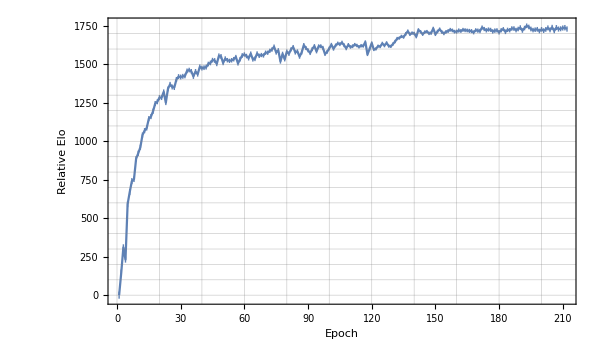

```mathematica
plot=ListLinePlot[#-#[[1,1]]&@(Around[Mean[#],StandardDeviation[#]]&/@Transpose@chain),PlotRange->{All,All},AspectRatio->0.6,Frame->True,FrameStyle->Directive[14,Black],ImagePadding->{{Automatic,10},{Automatic,10}},GridLines->All,FrameLabel->{"Epoch","Relative Elo"},ImageSize->600]
```

```mathematica
Export["./run5/elo-history.png",plot];
```

```mathematica
comparenets[{"run2",92},{"run3",123},400,4]
```

{185,15,200}

```mathematica
comparenets[{"run3",107},{"run5",218},800,4]
```

{410,31,359}

```mathematica
eloestimate[{457,14,329}]
```

56.12.

```mathematica
eloestimate[{135,20,245}]
```

-98.20.

```mathematica
eloestimate@{18,3,19}
```

-5.56.

```mathematica
eloestimate@{9,1,22}
```

-154.70.

```mathematica
eloestimate@{14,1,25}
```

-90.62.

### vs Edax

```mathematica
wait[process_,prompt_]:=Block[{str={""}},Do[Pause[0.05];If[!TrueQ[ProcessStatus[process]=="Running"],str={"",EndOfFile,""};Break[]];str=str~Join~StringSplit[ReadString[process,EndOfBuffer],"\n"];If[StringMatchQ[Last@str,prompt~~___],Break[]];,∞];str[[2;;-2]]];
sendandwait[process_,command_,prompt_]:=(WriteLine[process,command];wait[process,prompt])
boardempties[board_]:=StringCount[board,"-"];
edaxsearchboard[board_]:=(sendandwait[edax,"setboard "<>board,">"];
edaxstr=sendandwait[edax,"go",">"];
StringJoin@Flatten@StringCases[edaxstr,"Edax plays "~~square__~~EndOfString:>square])
neuralsearchboard[board_]:=(sendandwait[neural,"setboard "<>board,">"];
StringJoin[neuralstr=sendandwait[neural,"go",">"]])
neuralupdateboard[board_,move_]:=(sendandwait[neural,"setboard "<>board,">"];sendandwait[neural,"move "<>move,">"];sendandwait[neural,"textform "<>move,">"][[1]])
neuralgeteval[board_]:=(sendandwait[neural,"setboard "<>board,">"];sendandwait[neural,"eval",">"])
neural=StartProcess[{"./othello","--mode","interactive","--net-path","run2/nets/net-0038","--playouts","800","--midgame-temp","0.0"}];
edax=StartProcess[{"./lEdax-x64","-vv","-cpu","-book-usage","off","-level","3","-n-tasks","1"},ProcessDirectory->"/home/tlu/Documents/git/edax-reversi/bin"];wait[edax,">"];wait[neural,">"];
Echo[textboard0=RandomChoice@StringSplit[Import["openings.txt","Text"],"\n"]];
ismove[move_]:=Head[move]===String&&StringMatchQ[move,RegularExpression["[A-Ha-h][1-8]"]];
Do[
textboard=textboard0;
movehistory={};
result=Null;
Do[If[i>1||neuralmovesfirst,
textmove=neuralsearchboard[textboard];
If[(!ismove[textmove])&&(!ismove[Last@movehistory]),result=999;Break[];];
AppendTo[movehistory,textmove];
textboard=neuralupdateboard[textboard,textmove];
If[boardempties[textboard]≤6,result=neuralgeteval[textboard];Break[]];];
textmove=edaxsearchboard[textboard];
If[(!ismove[textmove])&&(!ismove[Last@movehistory]),result=999;Break[];];
AppendTo[movehistory,textmove];
textboard=neuralupdateboard[textboard,textmove];
If[boardempties[textboard]≤6,result=neuralgeteval[textboard];Break[]];,{i,60}];
Print[StringRiffle[movehistory," "]<>" "<>ToString[If[OddQ@Length@movehistory,-1,1]*If[neuralmovesfirst,1,-1]*ToExpression@result[[1]]]];
,{neuralmovesfirst,{True,False}}];
sendandwait[edax,"quit",">"];
sendandwait[neural,"quit",">"];
```